# Regularization

Ejemplo de "ill-possed" problem

```mathematica
data = {{0.,0.},{0.001,1},{0.01,1}};
```

```mathematica
data//MatrixForm
```

(0. | 0.
0.001 | 1
0.01 | 1)

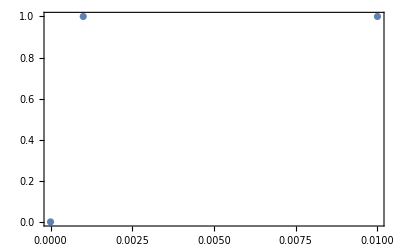

```mathematica
ListPlot[data,Frame->True,Axes->False]
```

```mathematica
ajuste=Fit[data,{1,x,x^2,x^3},x]
```

-8.06906×10^-16+1045.45 x-39991.1 x^2-5.45536×10^6 x^3

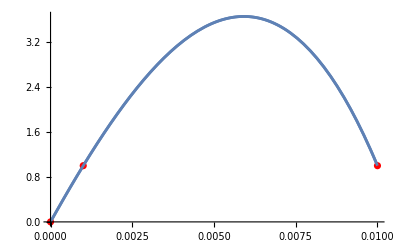

```mathematica
Show[Plot[ajuste,{x,0,0.01},PlotRange->All],ListPlot[data,Frame->True,Axes->False,PlotStyle->Red],Plot[ajuste,{x,0,0.01}]]
```

#### Otro ejemplo

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/michel/Library/CloudStorage/OneDrive-uv.cl/cursos/pregrado/Estadisticas/2024/Clases

```mathematica
dat= Import["fase_dB.csv"];
```

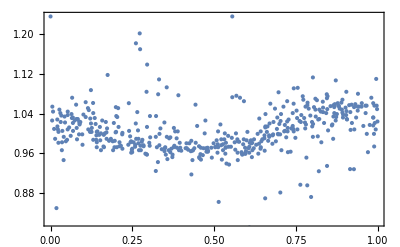

```mathematica
gr0=ListPlot[dat,Frame->True]
```

```mathematica
Length@dat
```

475

```mathematica
FindFormula[dat,x]
```

0.999188

```mathematica
FindFit[dat,a Sin[b+c x],{a,b,c},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→2.37394,b→0.428745,c→0.011303}

```mathematica
overfit=FindFormula[dat,x,SpecificityGoal->Infinity]
```

1.08921-6.29593 x-2022.75 x^3.-282839. x^7.-235180. x^9.+164.689 Abs[x]^2.+13917.8 Abs[x]^4.-58783.6 Abs[x]^5.+159459. Abs[x]^6.+326014. Abs[x]^8.+96418.5 Abs[x]^10.-17142.9 Abs[x]^11.

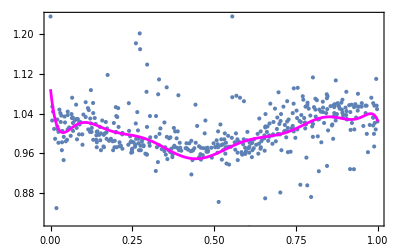

```mathematica
Show[gr0,Plot[overfit,{x,0,1},PlotStyle->Magenta]]
```

```mathematica
lm1=LinearModelFit[dat,{1,x},x]
```

FittedModel[…]

```mathematica
Normal[lm1]
```

0.986927+0.0244454 x

```mathematica
lm2=LinearModelFit[dat,{1,x,x^2},x]
```

FittedModel[…]

```mathematica
Normal[lm2]
```

1.03463-0.266767 x+0.293593 x^2

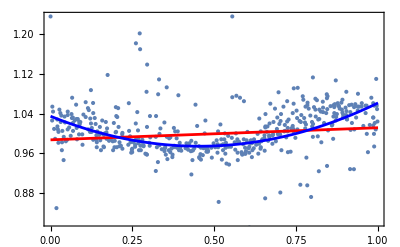

```mathematica
Show[ListPlot[dat],Plot[lm1[x],{x,0,1},PlotStyle->Red],Plot[lm2[x],{x,0,1},PlotStyle->Blue],Frame->True,Axes->False]
```

```mathematica
lm8=LinearModelFit[dat,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]
```

FittedModel[…]

```mathematica
Normal[lm8]
```

1.05163-1.80251 x+26.0318 x^2-164.664 x^3+525.109 x^4-931.518 x^5+940.73 x^6-507.954 x^7+114.053 x^8

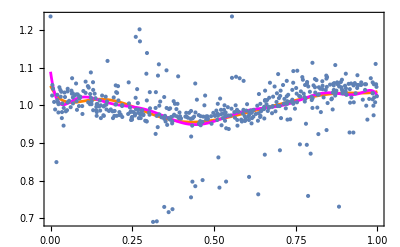

```mathematica
Show[Plot[{lm8[x],overfit},{x,0,1},PlotStyle->{Orange,Magenta},PlotRange->All],ListPlot[dat],Frame->True,Axes->False]
```

```mathematica
{lm1[x],lm2[x],lm8[x],overfit}/.x->0.001
```

{0.986951,1.03436,1.04985,1.08307}

lm8--> OVERFITTING

```mathematica
lm1["FitResiduals"][[1;;10]]
```

{-0.0379107,0.0130108,0.0406521,-0.0434356,-0.0381601,0.000574546,-0.0338643,0.0448987,0.0734506,0.0431648}

```mathematica
Table[dat[[k,2]]-lm1[x]/.x->dat[[k,1]],{k,Length@dat}][[1;;10]]
```

{-0.0379107,0.0130108,0.0406521,-0.0434356,-0.0381601,0.000574546,-0.0338643,0.0448987,0.0734506,0.0431648}

```mathematica
Chop[%-%%]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Total/@(#^2&/@{lm1["FitResiduals"],lm2["FitResiduals"],lm8["FitResiduals"]})
```

{1.89998,1.67581,1.60656}

### Tihkonov (Ridge) Regularization -> + Penalty function

### Modelo lineal

```mathematica
Clear[modelo1]
```

```mathematica
modelo1[x_]=a + b x;
```

Residual Sum of Squares (RSS)

```mathematica
rss1=Sum[(dat[[k,2]]-modelo1[dat[[k,1]]])^2,{k,Length[dat]}];
```

```mathematica
sol1=NMinimize[rss1,{a,b}]
```

{1.89998,{a→0.986927,b→0.0244454}}

```mathematica
ridge1=Sum[(dat[[k,2]]-modelo1[dat[[k,1]]])^2,{k,Length[dat]}]+ λ(a^2+b^2);
```

```mathematica
solT1=NMinimize[ridge1/.λ->1,{a,b}]
```

{2.86716,{a→0.979106,b→0.0359282}}

```mathematica
NMinimize[ridge1/.λ->.1,{a,b}]
```

{1.99737,{a→0.986126,b→0.0256286}}

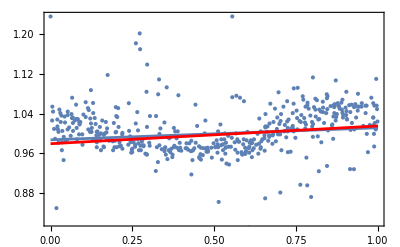

```mathematica
Show[ListPlot[dat],Plot[modelo1[x]/.sol1[[2]],{x,0,1}],Plot[modelo1[x]/.solT1[[2]],{x,0,1},PlotStyle->Red],Frame->True,Axes->False]
```

### Modelo cuadratico

```mathematica
Clear[modelo2]
```

```mathematica
modelo2[x_]=a + b x + c x^2;
```

Residual sum of squares

```mathematica
rss2=Sum[(dat[[k,2]]-modelo2[dat[[k,1]]])^2,{k,Length[dat]}];
```

```mathematica
sol2=NMinimize[rss2,{a,b,c}]
```

{1.67581,{a→1.03463,b→-0.266767,c→0.293593}}

```mathematica
ridge2=Sum[(dat[[k,2]]-modelo2[dat[[k,1]]])^2,{k,Length[dat]}]+ λ(a^2+b^2+c^2);
```

```mathematica
solT2=NMinimize[ridge2/.λ->1,{a,b,c}]
```

{2.77776,{a→0.999918,b→-0.098948,c→0.139675}}

```mathematica
Sum[(dat[[k,2]]-modelo2[dat[[k,1]]]/.solT2[[2]])^2,{k,Length[dat]}]+ λ(a^2+b^2+c^2)/.solT2[[2]]/.λ->1.
```

2.77776

```mathematica
Sum[(dat[[k,2]]-modelo2[dat[[k,1]]]/.solT2[[2]])^2,{k,Length[dat]}]
```

1.74863

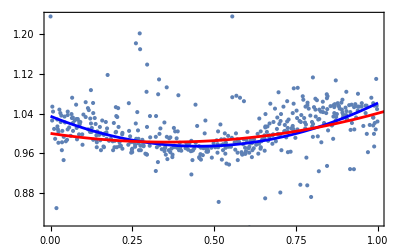

```mathematica
Show[ListPlot[dat],Plot[modelo2[x]/.sol2[[2]],{x,0,1},PlotStyle->Blue],Plot[modelo2[x]/.solT2[[2]],{x,0,5},PlotStyle->Red],Frame->True,Axes->False]
```

### Modelo “octavico”

```mathematica
Clear[modelo8]
```

```mathematica
modelo8[x_]=a0 + a1 x + a2 x^2 +a3 x^3 +a4 x^4 +a5 x^5 +a6 x^6 +a7 x^7 +a8 x^8 ;
```

Residual sum of squares

```mathematica
rss8=Sum[(dat[[k,2]]-modelo8[dat[[k,1]]])^2,{k,Length[dat]}];
```

```mathematica
sol8=NMinimize[rss8,{a0,a1,a2,a3,a4,a5,a6,a7,a8}]
```

{1.60656,{a0→1.05163,a1→-1.80251,a2→26.0317,a3→-164.663,a4→525.107,a5→-931.515,a6→940.726,a7→-507.951,a8→114.052}}

```mathematica
Clear[ridge8]
```

```mathematica
ridge8=Sum[(dat[[k,2]]-modelo8[dat[[k,1]]])^2,{k,Length[dat]}]+ λ(a0^2+a1^2+a2^2+a3^2+a4^2+a5^2+a6^2+a7^2+a8^2);
```

```mathematica
solT8=NMinimize[ridge8/.λ->1.,{a0,a1,a2,a3,a4,a5,a6,a7,a8}]
```

{2.73602,{a0→1.0038,a1→-0.0823764,a2→0.0104462,a3→0.0698043,a4→0.0696955,a5→0.0428099,a6→0.00871078,a7→-0.0240325,a8→-0.0523767}}

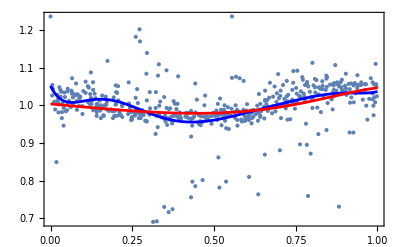

```mathematica
Show[ListPlot[dat],Plot[modelo8[x]/.sol8[[2]],{x,0,1},PlotStyle->Blue],Plot[modelo8[x]/.solT8[[2]],{x,0,1},PlotStyle->Red],Frame->True,Axes->False,PlotRange->All]
```

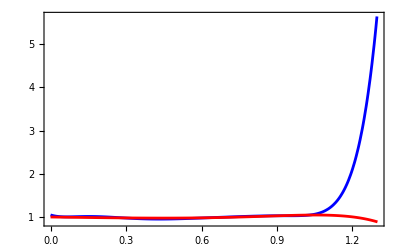

```mathematica
Show[Plot[modelo8[x]/.sol8[[2]],{x,0,1.5},PlotStyle->Blue],Plot[modelo8[x]/.solT8[[2]],{x,0,1.5},PlotStyle->Red],Frame->True,Axes->False,PlotRange->All]
```

### Modelo Sin

```mathematica
Clear[modeloS]
```

```mathematica
modeloS[x_]=a0 Sin[a1 + a2 x];
```

Residual sum of squares

```mathematica
rssS=Sum[(dat[[k,2]]-modeloS[dat[[k,1]]])^2,{k,Length[dat]}];
```

```mathematica
solS=FindMinimum[rssS,{{a0,.1},{a1,.5},{a2,.1}},MaxIterations->10000]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

{1.89998,{a0→422.94,a1→0.00233349,a2→0.000057799}}

```mathematica
solS=NMinimize[rssS,{{a0,.1,4.},{a1,.3,.5},{a2,1.,10.}},Method->"SimulatedAnnealing"]
```

{1.9,{a0→4.72105,a1→0.210603,a2→0.00529317}}

```mathematica
modeloS[x]/.solS[[2]]
```

4.86926 Sin[0.204101+0.00512514 x]

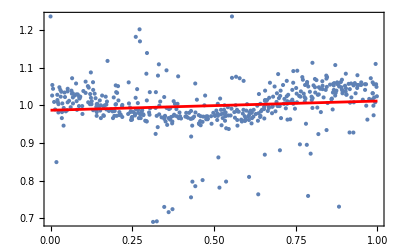

```mathematica
Show[ListPlot[dat],Plot[modeloS[x]/.solS[[2]],{x,0,1},PlotStyle->Red],Frame->True,Axes->False,PlotRange->All]
```

```mathematica
Clear[ridgeS]
```

```mathematica
ridgeS=Sum[(dat[[k,2]]-modeloS[dat[[k,1]]])^2,{k,Length[dat]}]+ λ(a0^2+a1^2+a2^2);
```

```mathematica
solTS=NMinimize[ridgeS/.λ->1.,{a0,a1,a2},Method->"SimulatedAnnealing"]
```

{4.26088,{a0→-1.18786,a1→-0.964816,a2→-0.0601}}

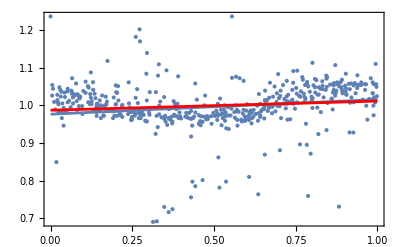

```mathematica
Show[ListPlot[dat],Plot[modeloS[x]/.solTS[[2]],{x,0,1}],Plot[modeloS[x]/.solS[[2]],{x,0,1},PlotStyle->Red],Frame->True,Axes->False,PlotRange->All]
```

### Regularización en Mathematica

```mathematica
?FitRegularization
```

```mathematica
Fit[dat,{1,x},x]
```

0.986927+0.0244454 x

```mathematica
tik1=Fit[dat,{1,x},x,FitRegularization->{"Tikhonov",1.}]
```

0.979106+0.0359282 x

```mathematica
modelo1[x]/.solT1[[2]]
```

0.979106+0.0359282 x

{"Tikhonov", λ} | regularize with λ||a(||)^2
{"LASSO",λ} | regularize with λ||a(||)_1
{"Variation",λ} | regularize with λ||Differencespaclet:ref/Differences[a](||)^2
{"TotalVariation",λ} | regularize with λ||Differencespaclet:ref/Differences[a](||)_1
{"Curvature",λ} | regularize with λ||Differencespaclet:ref/Differences[a,2](||)^2

```mathematica
lass1=Fit[dat,{1,x},x,FitRegularization->{"LASSO",1.}]
```

0.989027+0.0181585 x

```mathematica
rss1lasso=Sum[(dat[[k,2]]-modelo1[dat[[k,1]]])^2,{k,Length[dat]}]+ λ(Abs[a]+Abs[b]);
```

```mathematica
sol1L=NMinimize[rss1lasso/.λ->1,{{a,.1,1.},{b,.01,.1}},Method->"SimulatedAnnealing"]
```

{2.90926,{a→0.989027,b→0.0181584}}

```mathematica
modelo1[x]/.sol1L[[2]]
```

0.989027+0.0181584 x

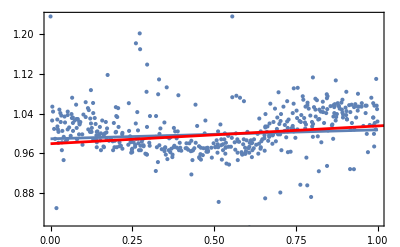

```mathematica
Show[ListPlot[dat],Plot[modelo1[x]/.sol1L[[2]],{x,0,1}],Plot[tik1,{x,0,5},PlotStyle->Red],Frame->True]
```

```mathematica
tik2=Fit[dat,{1,x,x^2},x,FitRegularization->{"Tikhonov",1.}]
```

0.999918-0.098948 x+0.139675 x^2

```mathematica
sol1L
```

{2.90926,{a→0.989027,b→0.0181584}}

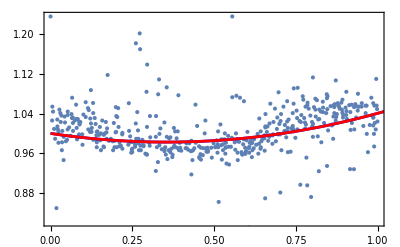

```mathematica
Show[ListPlot[dat],Plot[modelo2[x]/.solT2[[2]],{x,0,5},PlotStyle->Blue],Plot[tik2,{x,0,5},PlotStyle->Red],Frame->True]
```

```mathematica
tik8=Fit[dat,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x,FitRegularization->{"Tikhonov",1.}]
```

1.0038-0.0823764 x+0.0104462 x^2+0.0698043 x^3+0.0696955 x^4+0.0428099 x^5+0.00871078 x^6-0.0240325 x^7-0.0523767 x^8

```mathematica
modelo8[x]/.solT8[[2]]
```

1.0038-0.0823764 x+0.0104462 x^2+0.0698043 x^3+0.0696955 x^4+0.0428099 x^5+0.00871078 x^6-0.0240325 x^7-0.0523767 x^8

```mathematica
Chop[%%-%]
```

0

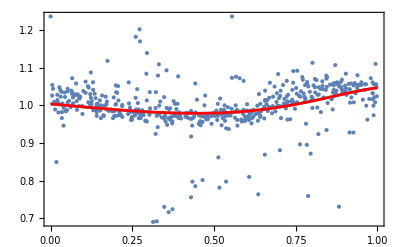

```mathematica
Show[ListPlot[dat],Plot[modelo8[x]/.solT8[[2]],{x,0,1}],Plot[tik8,{x,0,1},PlotStyle->Red],Frame->True,PlotRange->All]
```

{"Tikhonov", λ} | regularize with λ||a(||)^2
{"LASSO",λ} | regularize with λ||a(||)_1
{"Variation",λ} | regularize with λ||Differencespaclet:ref/Differences[a](||)^2
{"TotalVariation",λ} | regularize with λ||Differencespaclet:ref/Differences[a](||)_1
{"Curvature",λ} | regularize with λ||Differencespaclet:ref/Differences[a,2](||)^2

```mathematica
ridge8Variation=Sum[(dat[[k,2]]-modelo8[dat[[k,1]]])^2,{k,Length[dat]}]+ λ((a0-a1)^2+(a1-a2)^2+(a2-a3)^2+(a3-a4)^2+(a4-a5)^2+(a5-a6)^2+(a6-a7)^2+(a7-a8)^2);
```

```mathematica
solV8=NMinimize[ridge8Variation/.λ->1.,{a0,a1,a2,a3,a4,a5,a6,a7,a8}]
```

{2.70573,{a0→0.971823,a1→0.0935697,a2→-0.105594,a3→-0.0450203,a4→0.0411622,a5→0.0755625,a6→0.0549797,a7→0.00582395,a8→-0.0364995}}

```mathematica
solT8[[2]]
```

{a0→1.0038,a1→-0.0823764,a2→0.0104462,a3→0.0698043,a4→0.0696955,a5→0.0428099,a6→0.00871078,a7→-0.0240325,a8→-0.0523767}

```mathematica
tik8=Fit[dat,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x,FitRegularization->{"Variation",1.}]
```

0.971823+0.0935697 x-0.105594 x^2-0.0450203 x^3+0.0411622 x^4+0.0755625 x^5+0.0549797 x^6+0.00582395 x^7-0.0364995 x^8

```mathematica
modelo8[x]/.solV8[[2]]
```

0.971823+0.0935697 x-0.105594 x^2-0.0450203 x^3+0.0411622 x^4+0.0755625 x^5+0.0549797 x^6+0.00582395 x^7-0.0364995 x^8

## L - Curve para cálcular λ

The L - curve is a plot of the norm of a regularized solution versus the norm of the corresponding residual norm . It is a convenient graphical tool for displaying the trade - off between the size of a regularized solution and its fit to the given data, as the regularization parameter varies .
-Graphics-

## La Curva-L Modelo Lineal

Fitpaclet:ref/Fit[{m,v}]
finds a fit vector a that minimizes ||m.a-v|| for a design matrix m.
DesignMatrixpaclet:ref/DesignMatrix[{{x_11,x_12,…,y_1},{x_21,x_22,…,y_2},…},{f_1,f_2,…},{x_1,x_2,…}]constructs the design matrix for the linear model β_0+β_1 f_1+β_2 f_2+….

```mathematica
dat=Table[{x,1.5+ 3.2 x+RandomVariate[UniformDistribution[{-5,5}]]},{x,0,5,.5}];
```

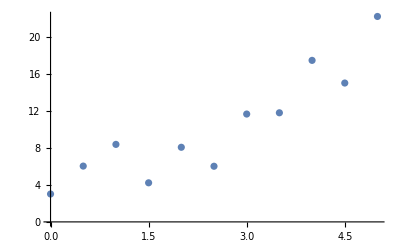

```mathematica
ListPlot[dat]
```

```mathematica
Clear[modelo1]
modelo1[x_]=a + b x;
```

```mathematica
A=DesignMatrix[dat,{1,x},x]
```

{{1.,0.},{1.,0.5},{1.,1.},{1.,1.5},{1.,2.},{1.,2.5},{1.,3.},{1.,3.5},{1.,4.},{1.,4.5},{1.,5.}}

```mathematica
A//MatrixForm
```

(1. | 0.
1. | 0.5
1. | 1.
1. | 1.5
1. | 2.
1. | 2.5
1. | 3.
1. | 3.5
1. | 4.
1. | 4.5
1. | 5.)

```mathematica
Dimensions@A
```

{11,2}

```mathematica
param={a,b}
```

{a,b}

```mathematica
A.param
```

{0.+1. a,1. a+0.5 b,1. a+1. b,1. a+1.5 b,1. a+2. b,1. a+2.5 b,1. a+3. b,1. a+3.5 b,1. a+4. b,1. a+4.5 b,1. a+5. b}

```mathematica
A.param//MatrixForm
```

(0.+1. a
1. a+0.5 b
1. a+1. b
1. a+1.5 b
1. a+2. b
1. a+2.5 b
1. a+3. b
1. a+3.5 b
1. a+4. b
1. a+4.5 b
1. a+5. b)

```mathematica
Length[A.param]
```

11

```mathematica
Total[#^2& /@(dat[[All,2]]-A.param)]
```

(3.01987-1. a)^2+(22.2328-1. a-5. b)^2+(15.0279-1. a-4.5 b)^2+(17.4804-1. a-4. b)^2+(11.8084-1. a-3.5 b)^2+(11.6721-1. a-3. b)^2+(6.0221-1. a-2.5 b)^2+(8.07564-1. a-2. b)^2+(4.23013-1. a-1.5 b)^2+(8.3878-1. a-1. b)^2+(6.03996-1. a-0.5 b)^2

```mathematica
(dat[[All,2]]-A.param).(dat[[All,2]]-A.param)
```

(3.01987-1. a)^2+(22.2328-1. a-5. b)^2+(15.0279-1. a-4.5 b)^2+(17.4804-1. a-4. b)^2+(11.8084-1. a-3.5 b)^2+(11.6721-1. a-3. b)^2+(6.0221-1. a-2.5 b)^2+(8.07564-1. a-2. b)^2+(4.23013-1. a-1.5 b)^2+(8.3878-1. a-1. b)^2+(6.03996-1. a-0.5 b)^2

```mathematica
%%==%
```

True

```mathematica
rss1=Sum[(dat[[k,2]]-modelo1[dat[[k,1]]])^2,{k,Length[dat]}]
```

(3.01987-a)^2+(22.2328-a-5. b)^2+(15.0279-a-4.5 b)^2+(17.4804-a-4. b)^2+(11.8084-a-3.5 b)^2+(11.6721-a-3. b)^2+(6.0221-a-2.5 b)^2+(8.07564-a-2. b)^2+(4.23013-a-1.5 b)^2+(8.3878-a-1. b)^2+(6.03996-a-0.5 b)^2

```mathematica
%==%%%
```

True

```mathematica
sol1=NMinimize[rss1,{a,b}]
```

{67.1236,{a→2.27031,b→3.23722}}

```mathematica
Fit[{A,dat[[All,2]]}]
```

{2.27031,3.23722}

```mathematica
Fit[{A,dat[[All,2]]},{"BestFitParameters","FitResiduals"}]
```

{{2.27031,3.23722},{-0.749557,-2.15103,-2.88027,2.89602,0.669125,4.34127,0.309919,1.79217,-2.26115,1.80991,-3.7764}}

```mathematica
lcurveVariation = Table[{smoothed, residual} = Fit[{A,dat[[All,2]]},{"BestFitParameters","FitResiduals"},FitRegularization->{"Variation",2^logλ}];Tooltip[{Norm[residual],Norm[Differences[smoothed]]},2.^logλ],{logλ,-10,20}];
```

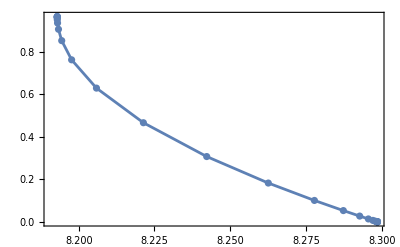

```mathematica
ListPlot[lcurveVariation,Joined->True,Mesh->All,Frame->True]
```

## La Curva-L Modelo Cuadratico

```mathematica
A=DesignMatrix[dat,{1,x,x^2},x];
```

```mathematica
A//MatrixForm
```

(1. | 0. | 0.
1. | 0.5 | 0.25
1. | 1. | 1.
1. | 1.5 | 2.25
1. | 2. | 4.
1. | 2.5 | 6.25
1. | 3. | 9.
1. | 3.5 | 12.25
1. | 4. | 16.
1. | 4.5 | 20.25
1. | 5. | 25.)

```mathematica
Dimensions@A
```

{11,3}

```mathematica
param={a,b,c}
```

{a,b,c}

```mathematica
A.param
```

{0.+1. a,1. a+0.5 b+0.25 c,1. a+1. b+1. c,1. a+1.5 b+2.25 c,1. a+2. b+4. c,1. a+2.5 b+6.25 c,1. a+3. b+9. c,1. a+3.5 b+12.25 c,1. a+4. b+16. c,1. a+4.5 b+20.25 c,1. a+5. b+25. c}

```mathematica
Length[A.param]
```

11

```mathematica
rss2=(dat[[All,2]]-A.param).(dat[[All,2]]-A.param);
```

```mathematica
sol1=NMinimize[rss2,{a,b,c}]
```

{42.569,{a→4.80786,b→-0.146177,c→0.67668}}

```mathematica
Fit[{A,dat[[All,2]]}]
```

{4.80786,-0.146177,0.67668}

```mathematica
Fit[{A,dat[[All,2]]},{"BestFitParameters","FitResiduals"}]
```

{{4.80786,-0.146177,0.67668},{1.78799,-1.13601,-3.04944,1.881,-0.853405,2.64957,-1.21261,0.777154,-2.43032,2.82493,-1.23885}}

```mathematica
lcurveVariation = Table[{smoothed, residual} = Fit[{A,dat[[All,2]]},{"BestFitParameters","FitResiduals"},FitRegularization->{"Variation",2^logλ}];Tooltip[{Norm[residual],Norm[Differences[smoothed]]},2.^logλ],{logλ,-10,20}];
```

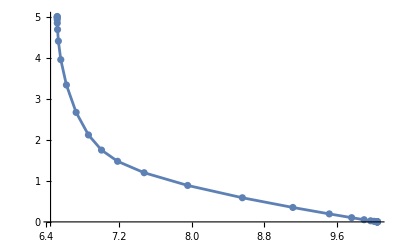

```mathematica
ListPlot[lcurveVariation,Joined->True,Mesh->All]
```

## La Curva-L Modelo “Octavico”

```mathematica
A=DesignMatrix[dat,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x];
```

```mathematica
A//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 0.5 | 0.25 | 0.125 | 0.0625 | 0.03125 | 0.015625 | 0.0078125 | 0.00390625
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1.5 | 2.25 | 3.375 | 5.0625 | 7.59375 | 11.3906 | 17.0859 | 25.6289
1. | 2. | 4. | 8. | 16. | 32. | 64. | 128. | 256.
1. | 2.5 | 6.25 | 15.625 | 39.0625 | 97.6563 | 244.141 | 610.352 | 1525.88
1. | 3. | 9. | 27. | 81. | 243. | 729. | 2187. | 6561.
1. | 3.5 | 12.25 | 42.875 | 150.063 | 525.219 | 1838.27 | 6433.93 | 22518.8
1. | 4. | 16. | 64. | 256. | 1024. | 4096. | 16384. | 65536.
1. | 4.5 | 20.25 | 91.125 | 410.063 | 1845.28 | 8303.77 | 37366.9 | 168151.
1. | 5. | 25. | 125. | 625. | 3125. | 15625. | 78125. | 390625.)

```mathematica
Dimensions@A
```

{11,9}

```mathematica
Clear[a,b,c,d,e,f,g,h,j]
```

```mathematica
param={a,b,c,d,e,f,g,h,j}
```

{a,b,c,d,e,f,g,h,j}

```mathematica
A.param
```

{0.+1. a,1. a+0.5 b+0.25 c+0.125 d+0.0625 e+0.03125 f+0.015625 g+0.0078125 h+0.00390625 j,1. a+1. b+1. c+1. d+1. e+1. f+1. g+1. h+1. j,1. a+1.5 b+2.25 c+3.375 d+5.0625 e+7.59375 f+11.3906 g+17.0859 h+25.6289 j,1. a+2. b+4. c+8. d+16. e+32. f+64. g+128. h+256. j,1. a+2.5 b+6.25 c+15.625 d+39.0625 e+97.6563 f+244.141 g+610.352 h+1525.88 j,1. a+3. b+9. c+27. d+81. e+243. f+729. g+2187. h+6561. j,1. a+3.5 b+12.25 c+42.875 d+150.063 e+525.219 f+1838.27 g+6433.93 h+22518.8 j,1. a+4. b+16. c+64. d+256. e+1024. f+4096. g+16384. h+65536. j,1. a+4.5 b+20.25 c+91.125 d+410.063 e+1845.28 f+8303.77 g+37366.9 h+168151. j,1. a+5. b+25. c+125. d+625. e+3125. f+15625. g+78125. h+390625. j}

```mathematica
Length[A.param]
```

11

```mathematica
rss8=(dat[[All,2]]-A.param).(dat[[All,2]]-A.param);
```

```mathematica
sol8=NMinimize[rss8,{a,b,c,d,e,f,g,h,j}]
```

{15.3801,{a→3.00871,b→-30.6485,c→167.648,d→-274.838,e→215.218,f→-91.7052,g→21.825,h→-2.72529,j→0.139011}}

```mathematica
Fit[{A,dat[[All,2]]}]
```

{3.00871,-30.6488,167.65,-274.84,215.22,-91.7059,21.8251,-2.72531,0.139012}

```mathematica
Fit[{A,dat[[All,2]]},{"BestFitParameters","FitResiduals"}]
```

{{3.00871,-30.6488,167.65,-274.84,215.22,-91.7059,21.8251,-2.72531,0.139012},{-0.0111582,0.10749,-0.465285,1.19165,-1.99943,2.29618,-1.82753,0.995188,-0.354778,0.0747466,-0.00706537}}

```mathematica
lcurveVariation = Table[{smoothed, residual} = Fit[{A,dat[[All,2]]},{"BestFitParameters","FitResiduals"},FitRegularization->{"Variation",2^logλ}];Tooltip[{Norm[residual],Norm[Differences[smoothed]]},2.^logλ],{logλ,-10,20}];
```

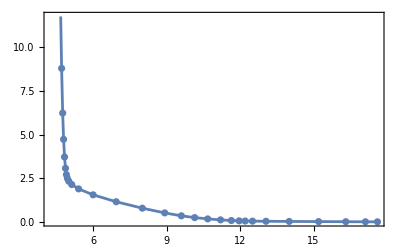

```mathematica
ListPlot[lcurveVariation,Joined->True,Mesh->All,Frame->True]
```

```mathematica
fitV8=Fit[{A,dat[[All,2]]},"BestFitParameters",FitRegularization->{"Variation",1}]
```

{3.5091,2.48496,0.999289,-0.180279,-0.581647,-0.192473,0.325767,-0.0910987,0.00766922}

```mathematica
Thread[param->fitV8]
```

{a→3.5091,b→2.48496,c→0.999289,d→-0.180279,e→-0.581647,f→-0.192473,g→0.325767,h→-0.0910987,j→0.00766922}

```mathematica
Clear[modelo8]
modelo8[x_]=a+ b x + c x^2 +d x^3 +e x^4 +f x^5 +g x^6 +h x^7 +j x^8 ;
```

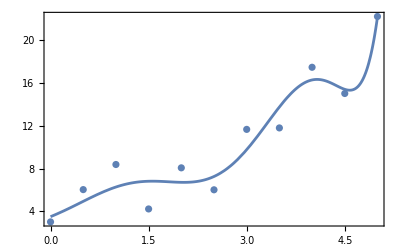

```mathematica
Show[ListPlot[dat,Frame->True,Axes->False],Plot[modelo8[x]/.Thread[param->fitV8],{x,0,5}],PlotRange->All]
```

```mathematica
rss8=Sum[(dat[[k,2]]-modelo8[dat[[k,1]]])^2,{k,Length[dat]}];
```

```mathematica
sol8=NMinimize[rss8,param]
```

{15.3801,{a→3.00871,b→-30.6485,c→167.648,d→-274.838,e→215.218,f→-91.7052,g→21.825,h→-2.72529,j→0.139011}}

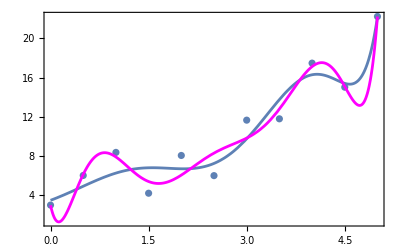

```mathematica
Show[ListPlot[dat,Frame->True,Axes->False],Plot[modelo8[x]/.Thread[param->fitV8],{x,0,5}],Plot[modelo8[x]/.sol8[[2]],{x,0,5},PlotStyle->Magenta],PlotRange->All]
```

## otro ejemplo mas

Smooth a corrupted signal using different  regularization methods:

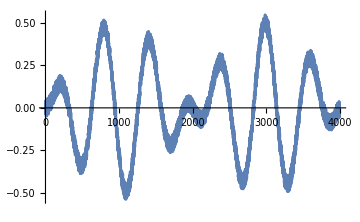

```mathematica
n = 4000;
times = N[Range[0,n-1]];
original = .5 Sin[2 Pi times/n]*Sin[.01 times];
corrupted = original + RandomReal[{-.05,.05},n];
ListLinePlot[corrupted,ImageSize->Medium]
```

Plot the tradeoff between the norm of the residuals and the norm of the variation:

```mathematica
id = IdentityMatrix[n];
```

```mathematica
lcurveVariation = Table[{smoothed, residual} = Fit[{id, corrupted},{"BestFitParameters","FitResiduals"},FitRegularization->{"Variation",2^logλ}];Tooltip[{Norm[Differences[smoothed]],Norm[residual]},2.^logλ],{logλ,-10,20}];
```

```mathematica
lcurveVariation
```

{{2.56703,0.00432588},{2.55962,0.00862384},{2.54494,0.0171372},{2.51616,0.0338413},{2.46084,0.0660192},{2.35832,0.125883},{2.18051,0.230488},{1.90425,0.395277},{1.53877,0.61872},{1.14183,0.871547},{0.788527,1.11149},{0.522851,1.31006},{0.348315,1.4605},{0.247292,1.56895},{0.196436,1.64548},{0.17398,1.6997},{0.164641,1.73997},{0.160224,1.7764},{0.156814,1.83193},{0.152167,1.97479},{0.144308,2.38105},{0.131158,3.33727},{0.111369,5.04565},{0.086106,7.39967},{0.0597067,9.9571},{0.0372553,12.1852},{0.0213443,13.7893},{0.0115324,14.7884},{0.0060142,15.3537},{0.0030756,15.6559},{0.00155688,15.8125}}

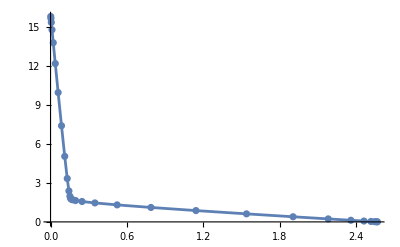

```mathematica
ListPlot[lcurveVariation,Joined->True,Mesh->All]
```

```mathematica
smoothed= Fit[{id, corrupted},"BestFitParameters",FitRegularization->{"Variation",128}];
```

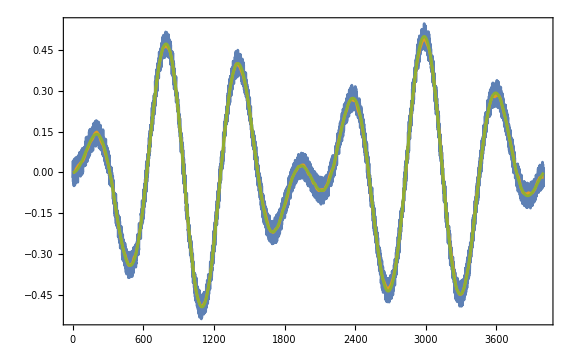

```mathematica
ListLinePlot[{ corrupted,smoothed,original},Frame->True,ImageSize->Large]
```

## Ajuste Robusto

```mathematica
Clear["`*"];
```

```mathematica
datos= Import["fase_dB.csv"];
```

```mathematica
dat=RandomChoice[datos,10];
```

```mathematica
lm2=Fit[dat,{1,x,x^2},x]
```

1.1047933306494754-0.58242385639852377 x+0.65670082870523446 x^2

```mathematica
gr0=ListPlot[dat,Frame->True];
```

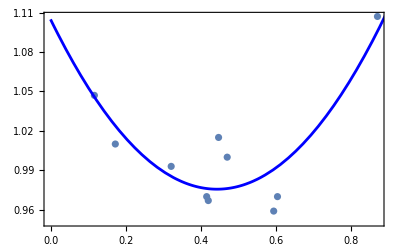

```mathematica
Show[gr0,Plot[lm2,{x,0,1},PlotStyle->Blue],Frame->True,Axes->False]
```

```mathematica
lm2R=Fit[dat,x^Range[0,3,1],x,NormFunction->{"HuberPenalty",.1}]
```

1.03416+0.0956358 x-0.989862 x^2+1.11674 x^3

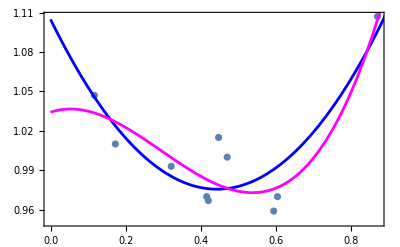

```mathematica
Show[gr0,Plot[{lm2,lm2R},{x,0,1},PlotStyle->{Blue,Magenta}],Frame->True,Axes->False]
```